```mathematica
Clear["Global`*"]

aopen = 45/100;
aclosed = 55/100;
b=1/20;
Xrot=-1/4;
L = 1;
U=1;
DX=1/10;
DY=1/10;
Dyy[θ_]:=DX*Sin[θ]^2+DY*Cos[θ]^2;

ζminusopen[θ_]:=Sqrt[aopen^2 * Sin[θ]^2 + b^2 * Cos[θ]^2]+Xrot*Sin[θ]-L/2;
ζplusopen [θ_]:=-Sqrt[aopen^2 * Sin[θ]^2 + b^2 * Cos[θ]^2]+Xrot*Sin[θ]+L/2;

ζminusclosed[θ_]:=Sqrt[aclosed^2 * Sin[θ]^2 + b^2 * Cos[θ]^2]+Xrot*Sin[θ]-L/2;
ζplusclosed[θ_]:=-Sqrt[aclosed^2 * Sin[θ]^2 + b^2 * Cos[θ]^2]+Xrot*Sin[θ]+L/2;

σ[θ_]:=U*Sin[θ]/Dyy[θ];
```

```mathematica
ηopen[θ_]:=(Exp[σ[θ]ζplusopen[θ]]-Exp[σ[θ]ζminusopen[θ]]); (* Note that this is not of the same form to avoid dividing by 0*)
ηclosed[θ_]:=(Exp[σ[θ]ζplusclosed[θ]]-Exp[σ[θ]ζminusclosed[θ]]);

νopen[θ_]:=((ηopen[θ]/σ[θ])-ζplusopen[θ]Exp[σ[θ]ζplusopen[θ]]+ζminusopen[θ]Exp[σ[θ]ζminusopen[θ]])σ'[θ];
νclosed[θ_]:=((ηclosed[θ]/σ[θ])-ζplusclosed[θ]Exp[σ[θ]ζplusclosed[θ]]+ζminusclosed[θ]Exp[σ[θ]ζminusclosed[θ]])σ'[θ];
```

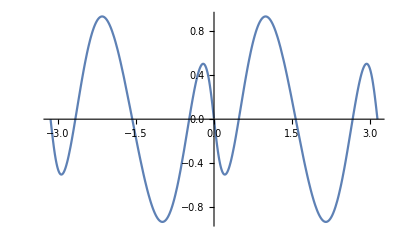

```mathematica
Plot[νopen[ϕ]/ηopen[ϕ],{ϕ,-π,π}]
```

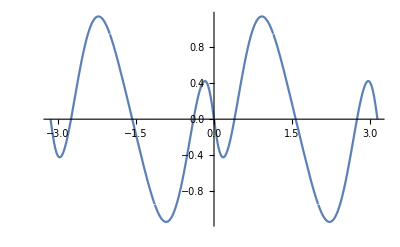

```mathematica
Plot[νclosed[ϕ]/ηclosed[ϕ],{ϕ,-π,π}]
```

```mathematica
θL = FindRoot[ζminusclosed[θ]==ζplusclosed[θ],{θ, -0.6}]
```

{θ→-1.13919}

```mathematica
θR = FindRoot[ζminusclosed[θ]==ζplusclosed[θ],{θ, 0.6}]
```

{θ→1.13919}

```mathematica
fopen[θ_]:=NIntegrate[νopen[ϕ]/ηopen[ϕ],{ϕ,-π,θ}, MaxRecursion->20,WorkingPrecision->20, Method->{GlobalAdaptive,MaxErrorIncreases->10000}];
fclosed[θ_]:=NIntegrate[νclosed[ϕ]/ηclosed[ϕ],{ϕ,-1.13919,θ}, MaxRecursion->20,WorkingPrecision->20, Method->{GlobalAdaptive,MaxErrorIncreases->10000}];

ρopen[θ_,y_]:=Exp[fopen[θ]+σ[θ]*y];
ρclosed[θ_,y_]:=Exp[fclosed[θ]+σ[θ]*y];

Ωopen =ImplicitRegion[(y<=ζplusopen[θ] && y>=ζminusopen[θ]), {{θ, -Pi, Pi}, y }];
Ωclosed =ImplicitRegion[(y<=ζplusclosed[θ] && y>=ζminusclosed[θ]), {{θ, -1.13919, 1.13919}, y }];
Ωclosed2 =ImplicitRegion[(y<=ζplusclosed[θ] && y>=ζminusclosed[θ]), {{θ, -Pi, Pi}, y }];
```

```mathematica
RegionPlot[Ωopen, FrameLabel->{θ,y} ,FrameTicks->{{Automatic,None},{{-Pi,-Pi/2, 0,Pi/2, Pi}, None}}]
```

-Graphics-

/Users/timwallace/Desktop/Test.png

```mathematica
RegionPlot[Ωclosed2, FrameLabel->{θ,y},FrameTicks->{{Automatic,None},{{-Pi,-Pi/2, 0,Pi/2, Pi}, None}}]
```

-Graphics-

```mathematica
RegionPlot[Ωclosed]
```

-Graphics-

```mathematica
ρopen[y_,θ_]:=Exp[fopen[θ]+σ[θ]y];
ρclosed[y_,θ_]:=Exp[fclosed[θ]+σ[θ]y];
```

```mathematica
Zopen = NIntegrate[ρopen[y,θ],{θ,-π,π},{y,ζminusopen[θ],ζplusopen[θ]}] ;
```

1.73343

```mathematica
Zclosed = NIntegrate[ρclosed[y,θ],{θ, -1.13919, 1.13919},{y,ζminusclosed[θ],ζplusclosed[θ]}];
```

NIntegrate::nlim: ϕ = θ is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

```mathematica
(*Zopen = 1.73343*)
(*Zclosed = *)
```

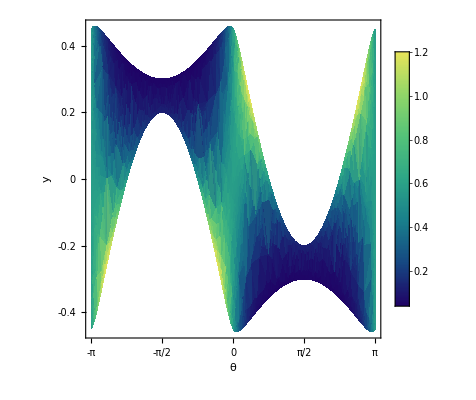

```mathematica
openfigure = DensityPlot[ρopen[y,θ]/1.73343,{θ,y}∈Ωopen,Frame->True,FrameTicks->{{{-0.4,-0.2,0,0.2,0.4},None},{{-π,-π/2,0,π/2,π},None}},FrameLabel->{θ,y},ColorFunction->"BlueGreenYellow",PlotLegends->Automatic]
```

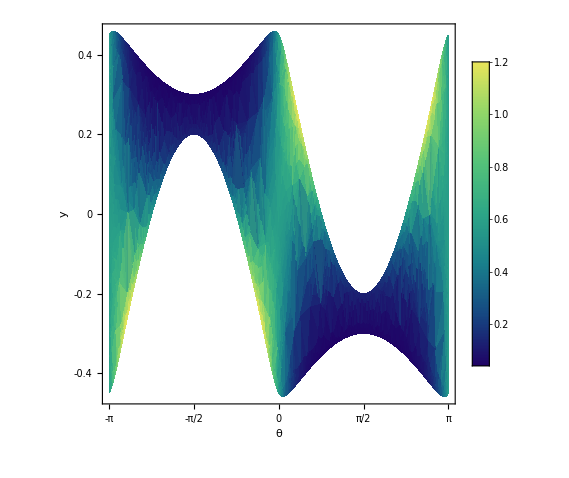

```mathematica
Export["/Users/timwallace/Desktop/Part III Maths/ABP-code/invariantdensityopen.png",openfigure,"PNG",ImageResolution->900]
```

/Users/timwallace/Desktop/Part III Maths/ABP-code/invariantdensityopen.png

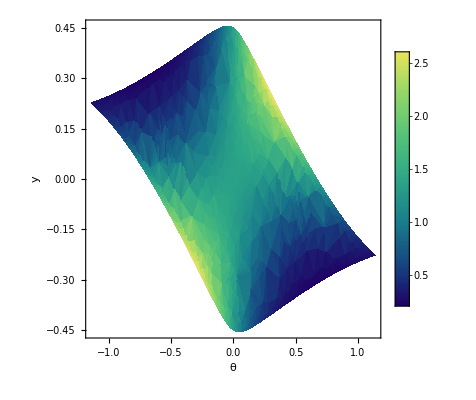

```mathematica
closedfigure =  DensityPlot[ρclosed[y,θ]/Zclosed,{θ,y}∈Ωclosed,Frame->True,FrameTicks->Automatic,FrameLabel->{θ,y},ColorFunction->"BlueGreenYellow",PlotLegends->Automatic]
```

```mathematica
Export["/Users/timwallace/Desktop/Part III Maths/ABP-code/invariantdensityclosed.png",closedfigure,"PNG",ImageResolution->900]
```

/Users/timwallace/Desktop/Part III Maths/ABP-code/invariantdensityclosed.png